```mathematica
ClearAll["Global`*"]
```

Implementation of the local dimension metric proposed by Lucarini et al. (2016) and application on the Lorenz system.

V. Lucarini et al.,Extremes and Recurrence in DynamicalSystems(Pure and Applied Mathematics: A Wiley Seriesof Texts, Monographs and Tracts (Wiley), 2016).

For an application on climate data see Davide’s paper: 
D. Faranda et al., Dynamical proxies of North Atlantic predictability and extremes, Sci. Rep.7, 41278 (2017).

#### Simulation of the system

```mathematica
(*variables*)
vars={x[t],y[t],z[t]};

(*parameters*)
σ=10;r=28;b=8/3;

(*Lorenz system*)
f=σ(y[t]-x[t]);
g=r x[t]-y[t]-x[t]z[t];
h=x[t] y[t]-b z[t];
eqns={x'[t]==f,y'[t]==g,z'[t]==h};

(*Initial conditions*)
inits={x[0]==0,y[0]==-1/100,z[0]==9};

(*Integrate forward in time*)
(sol={sx,sy,sz}=vars/.NDSolve[Join[eqns,inits],vars,{t,0,260,0.01},WorkingPrecision->50,PrecisionGoal->15,AccuracyGoal->15,MaxSteps->130000]⟦1⟧);
```

Let’s see the solution

```mathematica
xt=Table[sol[[1]],{t,0,260,0.01}];
yt=Table[sol[[2]],{t,0,260,0.01}];
zt=Table[sol[[3]],{t,0,260,0.01}];
```

```mathematica
orbit=Transpose[{xt,yt,zt}];
```

```mathematica
Graphics3D[{PointSize[0.001],Line[orbit]},Axes->True,AxesLabel->{"x","y","z"},AxesStyle->Directive[Black, 16],ImageSize->Large]
```

-Graphics3D-

```mathematica
Dimensions[orbit]
```

{26001,3}

#### Estimating the local dimension

```mathematica
(*Removing a (very long) transient*)
(*Just want to keep few time steps*)
orbit=orbit[[16000;;All]];
```

```mathematica
(*local dimension for a state ζ = x(τ)*)
dim[state_,orbit_,q_]:=
Module[
{observable,threshold,recurrences,dim,μ,σ},
observable=
Select[-Log[Table[EuclideanDistance[state,orbit[[i]]],{i,1,Length[orbit]}]],NumberQ[#]&];
threshold=Quantile[observable,q];
recurrences=Cases[observable,x_/;x>threshold];
dim=1/EstimatedDistribution[recurrences,ParetoPickandsDistribution[μ,σ,0]][[2]];
dim
]
```

```mathematica
q=0.96;
localDim=Table[dim[orbit[[i]],orbit,q],{i,1,Length[orbit]}];
```

```mathematica
Mean[localDim]
```

2.06113

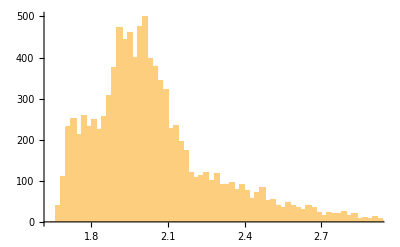

```mathematica
Histogram[localDim,100]
```